## Introduction



```mathematica
Plot[Sin[x],{x,0,10}]
```

```mathematica
Solve[x^2+3 x-2==0,x]//N
```

{{x→-3.56155},{x→0.561553}}

```mathematica
matr={{1,2},{3,4}};
```

```mathematica
matr//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
Eigenvalues[matr]
```

{1/2 (5+√33),1/2 (5-√33)}

## Document structure

### subsection 1

#### subsubsection

```mathematica
Plot[Sin[x],{x,0,10}]
```

-Graphics-

### subsection 2

#### subsection 3

## Head, FullForm

```mathematica
expr=Sin[x]+Cos[y]
```

Cos[y]+Sin[x]

```mathematica
expr//FullForm
```

Plus[Cos[y],Sin[x]]

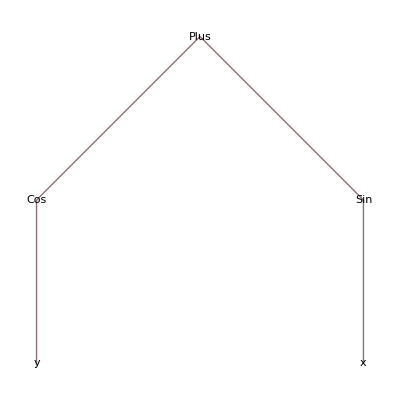

```mathematica
expr//TreeForm
```

```mathematica
expr//Head
```

Plus

```mathematica
Sin[x]//Head
```

Sin

```mathematica
x//Head
```

Symbol

```mathematica
1.245//Head
```

Real

```mathematica
23//Head
```

Integer

## Programming

### If, For

```mathematica
For[i=0,i≤5,i++,
Print[i];
Print[i+10,"\n"]
]
```

0

10

1

11

2

12

3

13

4

14

5

15

```mathematica
For[i=0,i≤5,i++,
If[i<3,
Print[i],
Print[i+10]
]
]
```

0

1

2

13

14

15

### User’s functions

```mathematica
f[x_]:=x^2+2 x+1;
```

```mathematica
f[3]
```

16

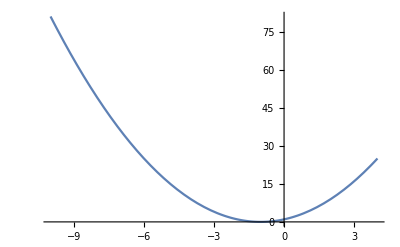

```mathematica
Plot[f[x],{x,-10,4}]
```

```mathematica
Clear[f];
f[x_]:=f[x]=x^2+2 x+1;
```

```mathematica
f[4]
```

25

```mathematica
??f
```

Global`f

f[x_]:=f[x]=x^2+2 x+1

### List

```mathematica
a={1,2,3}
```

{1,2,3}

```mathematica
Join[a,b]
```

{1,2,3,1,2,v}

```mathematica
Union[a,b]
```

{1,2,3,v}

```mathematica
a[[3]]
```

3

```mathematica
a//FullForm
```

List[1,2,3]

```mathematica
b={1,2,v}
```

{1,2,v}

```mathematica
a+b
```

{2,4,3+v}

```mathematica
a*0
```

{0,0,0}

```mathematica
Length[a]
```

3

```mathematica
m1=Table[i,{i,0,5,2}]
```

{0,2,4}

```mathematica
m2=Table[i+10j,{i,0,5},{j,2,3}]
```

{{20,30},{21,31},{22,32},{23,33},{24,34},{25,35}}

```mathematica
m2[[3,1]]
```

22

```mathematica
TableForm[m2]
```

20 | 30
21 | 31
22 | 32
23 | 33
24 | 34
25 | 35

читайте guides!!

### Listable functions, Map

```mathematica
m1={0,{1,2},3}
```

{0,{1,2},3}

```mathematica
MyFunction/@ m1
```

{MyFunction[0],MyFunction[{1,2}],MyFunction[3]}

```mathematica
Map[MyFunction,m1]
```

{MyFunction[0],MyFunction[2],MyFunction[4]}

```mathematica
Sin/@m1
```

{0,Sin[2],Sin[4]}

```mathematica
Sin[m1]
```

{0,{Sin[1],Sin[2]},Sin[3]}

## Equations

### Solve, NSolve

```mathematica
sol1=Solve[x^3+x^2+2 x-3== 0,x]
```

{{x→1/3 (-1-5 (2/(97+3 √1101))^(1/3)+(1/2 (97+3 √1101))^(1/3))},{x→-1/3-1/6 (1+ⅈ √3) (1/2 (97+3 √1101))^(1/3)+(5 (1-ⅈ √3))/(3 2^(2/3) (97+3 √1101)^(1/3))},{x→-1/3-1/6 (1-ⅈ √3) (1/2 (97+3 √1101))^(1/3)+(5 (1+ⅈ √3))/(3 2^(2/3) (97+3 √1101)^(1/3))}}

```mathematica
sol1[[1]]
```

{x→1/3 (-1-5 (2/(97+3 √1101))^(1/3)+(1/2 (97+3 √1101))^(1/3))}

```mathematica
x1=x/.sol1[[1]]
```

1/3 (-1-5 (2/(97+3 √1101))^(1/3)+(1/2 (97+3 √1101))^(1/3))

```mathematica
x1//N
```

0.843734

```mathematica
sol2=NSolve[x^3+x^2+2 x-3== 0,x]
```

{{x→-0.921867-1.64493 ⅈ},{x→-0.921867+1.64493 ⅈ},{x→0.843734}}

```mathematica
sol1//N
```

{{x→0.843734},{x→-0.921867-1.64493 ⅈ},{x→-0.921867+1.64493 ⅈ}}

### DSolve, NDSolve

```mathematica
DSolve[{y'[t]==y[t],y[1]==1},y[t],t]
```

{{y[t]→ⅇ^(-1+t)}}

```mathematica
sol1=NDSolve[{y'[t]==y[t],y[0]==1},y,{t,0,5}][[1]]
```

{y→InterpolatingFunction[{{0., 5.}}, <>]}

```mathematica
y[3]/.sol1
```

20.0855

```mathematica
Exp[3]//N
```

20.0855

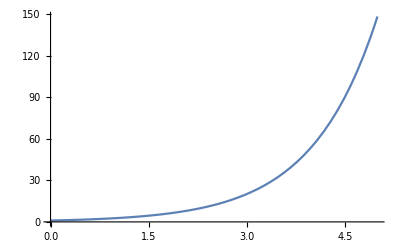

```mathematica
Plot[y[t]/.sol1,{t,0,5}]
```

## Block

```mathematica
g[x_,a_]:=x^2+2x+a;
```

```mathematica
a0=-1;
```

```mathematica
sol=Solve[g[x,a0]==0,x]
```

{{x→-1-√2},{x→-1+√2}}

```mathematica
x1=x/.sol[[1]]
```

-1-√2

```mathematica
x2=x/.sol[[2]]
```

-1+√2

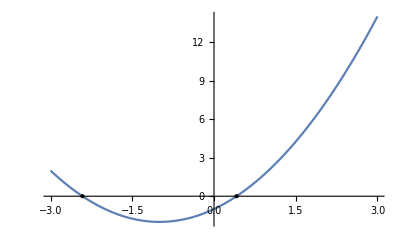

```mathematica
Plot[g[x,a0],{x,-3,3},Epilog->Point/@{{x1,0},{x2,0}}]
```

```mathematica
Clear[FirstRoot];
FirstRoot[a_]:=Block[{sol,x1,x2},
sol=Solve[g[x,a]==0,x];
x1=x/.sol[[1]];
x2=x/.sol[[2]];
Print["Первый корень ",x1];
Plot[g[x,a],{x,-3,3},Epilog->Point/@{{x1,0},{x2,0}}]
]
```

```mathematica
FirstRoot[-1]
```

Первый корень -1-√2

-Graphics-